# 4基盤ログの解析:推定ユーザーごとのアクセス推移（ユーザーストーリー）

-Graphics-

グラフ分析部分のみ、save済みグラフを読み込む。

## 準備

```mathematica
start=AbsoluteTime[Date[]]
```

3.910108815381312×10^9

#### 変数

```mathematica
date="20231110"
```

20231110

```mathematica
case={"ci","cs","la","wk"}
```

{ci,cs,la,wk}

```mathematica
base["ci"]="T=ci.P~5"
base["cs"]="T=cs.R=.P="
base["la"]="T=la.T~ea.A~hc.A~go.A~bot.P~api"
base["wk"]="T=wk.P~4.A~bot"
base["all"]="T=4"
```

T=ci.P~5

T=cs.R=.P=

T=la.T~ea.A~hc.A~go.A~bot.P~api

T=wk.P~4.A~bot

T=4

```mathematica
mountdir="/Volumes/home/NII/togo-log/rcoslogs/"
```

/Volumes/home/NII/togo-log/rcoslogs/

```mathematica
vocdir=mountdir<>"voc"
```

/Volumes/home/NII/togo-log/rcoslogs/voc

#### 解析用データ

```mathematica
fileliststr=Import[mountdir<>"log/D="<>date<>"/"<>"filenames","String"]
```

log-20231110.rcoslog0003.log

```mathematica
filelist=StringSplit[fileliststr]
```

{log-20231110.rcoslog0003.log}

元ログの大きさ （wc）

```mathematica
logwc=Import[mountdir<>"log/D="<>date<>"/logfiles.wc","String"]
```

20753167 285931395 9385127220 log-20231110.rcoslog0003.log

```mathematica
ckanfile=mountdir<>"crid/CIRDEV-1067_crid_list/ckan_product_crid_list.txt"
```

/Volumes/home/NII/togo-log/rcoslogs/crid/CIRDEV-1067_crid_list/ckan_product_crid_list.txt

```mathematica
ckanSt=Import[ckanfile,"String"];
```

```mathematica
(ckanName=StringSplit[ckanSt,"\n"])//Dimensions
```

{92643}

```mathematica
(ckanCridAC=Apply[Association,Map[#->#&,ckanName]])//Dimensions
```

{92643}

#### プログラム

vertexを指定してdirected-edgeを辿る部分グラフ抽出の関数：

```mathematica
directedConnectedGraphComponent[g_,v_]:=Module[{vAll,vOther,addEdge},
vAll=VertexList[g];
vOther=Complement[vAll,{v}];
addEdge=Map[#->v&,vOther];
Subgraph[g,ConnectedComponents[Flatten[{EdgeList[g],addEdge},1],v][[1]]]
]
```

グラフよりinがないノードを検出してそこから(g,v)に対して上記関数をアプライする関数：

```mathematica
vertexInGraph[g_Graph]:=Module[{deg,pos,vname},
deg=VertexInDegree[g];
pos=Position[deg,0]//Flatten//Union;
vname=VertexList[g][[pos]];
Map[directedConnectedGraphComponent[g,#]&,vname]
]
vertexInGraph[g_Integer]:=g
```

story-group-indexを各グラフにdistributeする関数：

```mathematica
distributeIdxGr[idxGr_]:=Module[
{date,idx,gr},
date=idxGr[[1]];
idx=idxGr[[2]];
gr=idxGr[[3]];
Map[{date,idx,#}&,gr]
]
```

stringからfqdnのみ抽出する関数：

```mathematica
fqdnFromPath[s_]:=StringJoin[StringSplit[s,"/"]⟦{1,3}⟧]
```

```mathematica
fqdnFromGraph[g_Graph]:=Union[Sort[Map[fqdnFromPath,VertexList[g]]]]
```

## Analysis

### Get graph

```mathematica
savedir=mountdir<>"log/D="<>date<>"/T=4/_story"
```

/Volumes/home/NII/togo-log/rcoslogs/log/D=20231110/T=4/_story

```mathematica
Get[savedir<>"/storyGrIdxFlDs3.save"];
```

### Analysis 1 graph property

基本属性

エッジ:

```mathematica
(eltbl[4]=Table[EdgeList[storyGrIdxFlDs3[4][[i]][[3]]],{i,Length[storyGrIdxFlDs3[4]]}])//Dimensions
```

{158476}

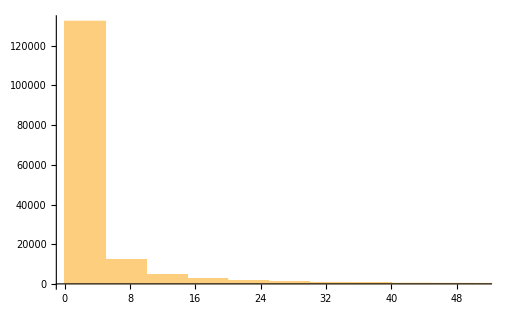

```mathematica
Histogram[Map[Length,eltbl[4]],{5}]
```

ノード:

```mathematica
(vltbl[4]=Table[VertexList[storyGrIdxFlDs3[4][[i]][[3]]],{i,Length[storyGrIdxFlDs3[4]]}])//Dimensions
```

{158476}

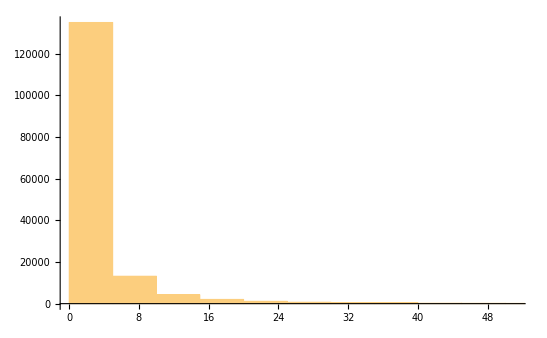

```mathematica
Histogram[Map[Length,vltbl[4]],{5}]
```

アクセス時刻:

```mathematica
(acct[4]=Map[#[[3,1]]&,eltbl[4],{2}])//Dimensions
```

{158476}

滞留時間：

```mathematica
(accspanMin[4]=Map[Max[#]-Min[#]&,acct[4]]/60)//Dimensions
```

{158476}

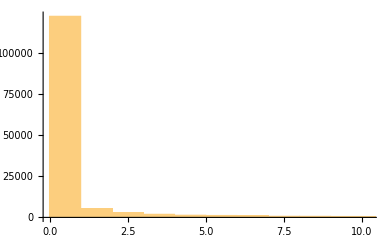

```mathematica
Histogram[accspanMin[4],{1}]
```

スタートノードが最小時刻になっていない。調整が必要か？

E/V ratio:

```mathematica
(ratioEV[4]=Map[Length,eltbl[4]]/Map[Length,vltbl[4]]//N)//Dimensions
```

{158476}

TV ratio :

```mathematica
(ratioTV[4]=acct[4]/Map[Length,vltbl[4]])//Dimensions
```

{158476}

TE ratio:

```mathematica
(ratioTE[4]=acct[4]/Map[Length,eltbl[4]])//Dimensions
```

{158476}

### Analysis 2 base interaction

リクエストパスから基盤名だけをとりだし、基盤連携を見る。

```mathematica
(GrBases[4]=Map[fqdnFromGraph[#[[3]]]&,storyGrIdxFlDs3[4]])//Dimensions
```

Part::partw: Part {1,3} of {} does not exist.

StringJoin::string: String expected at position 1 in StringJoin[{}⟦{1,3}⟧].

Part::partw: Part {1,3} of {} does not exist.

StringJoin::string: String expected at position 1 in StringJoin[{}⟦{1,3}⟧].

Part::partw: Part {1,3} of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

StringJoin::string: String expected at position 1 in StringJoin[{}⟦{1,3}⟧].

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

{158476}

NII基盤(4基盤以外も)へのアクセスを見る。

```mathematica
niidnpos=Flatten[Position[Map[StringMatchQ[#,RegularExpression[".*nii.ac.jp.*"]]||StringMatchQ[#,RegularExpression[".*jdcat.jsps.go.jp.*"]]&,Flatten[GrBases[4]]//Union],True]]
```

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[StringJoin[{}⟦{1,3}⟧],RegularExpression[.*nii.ac.jp.*]].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[StringJoin[{}⟦{1,3}⟧],RegularExpression[.*jdcat.jsps.go.jp.*]].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[StringJoin[{18.177.4.229}⟦{1,3}⟧],RegularExpression[.*nii.ac.jp.*]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

{35,40,41,44,49,73,79,102,168,173,188,202,238,239,241,242,243,244,245,258,283,284,312,330,373,397,399,421,424,435,443,466,601,699,708,717,794,824,825,827,839,1069,1086,1438,1546}

```mathematica
(Flatten[GrBases[4]]//Union)[[niidnpos]]
```

{http:binder.cs.rcos.nii.ac.jp,http:ci.nii.ac.jp,http:cir.nii.ac.jp,http:dashboard.la.lms.nii.ac.jp,http:dsr.nii.ac.jp,http:jdcat.jsps.go.jp,http:jupyter.cs.rcos.nii.ac.jp,http:lms.nii.ac.jp,https:alb-ci-nii-ac-jp-263480797.ap-northeast-1.elb.amazonaws.com:443,https:analytics.la.lms.nii.ac.jp,https:auth.cir.nii.ac.jp,https:binder.cs.rcos.nii.ac.jp,https:ci.nii.ac.jp,https:ci.nii.ac.jp:443,https:cir.nii.ac.jp,https:cir-nii-ac-jp.hit-u.idm.oclc.org,https:cir-nii-ac-jp.musashino-u.remotexs.co,https:cir-nii-ac-jp.nanzan-u.idm.oclc.org,https:cir-nii-ac-jp.translate.goog,https:core.orthros.gakunin.nii.ac.jp,https:dsc.repo.nii.ac.jp,https:ds.gakunin.nii.ac.jp,https:feedback.cir.nii.ac.jp,https:ge.nii.ac.jp:443,https:hosei.repo.nii.ac.jp,https:idp.nii.ac.jp,https:idp.rdm.nii.ac.jp,https:jdcat.jsps.go.jp,https:jgssdds.repo.nii.ac.jp,https:jupyter.cs.rcos.nii.ac.jp,https:kaken.nii.ac.jp,https:kobegakuin.repo.nii.ac.jp,https:lms.nii.ac.jp,https:niph.repo.nii.ac.jp,https:nwec.repo.nii.ac.jp,https:omnh.repo.nii.ac.jp,https:openidp.nii.ac.jp,https:rcos.nii.ac.jp,https:rcos.rdm.nii.ac.jp,https:rdm.nii.ac.jp,https:rissho.repo.nii.ac.jp,https:support.nii.ac.jp,https:tcu.repo.nii.ac.jp,https:www.nii.ac.jp,https:www.unii.ac.jp}

```mathematica
niigrp=".*\\.nii\\.ac\\.jp.*"
```

.*\.nii\.ac\.jp.*

```mathematica
(GrNiiBases[4]=Map[Cases[#,x_/;StringMatchQ[x,RegularExpression[niigrp]]||StringMatchQ[x,RegularExpression[".*jdcat.jsps.go.jp.*"]]]&,GrBases[4]])//Dimensions
```

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[StringJoin[{}⟦{1,3}⟧],RegularExpression[.*\.nii\.ac\.jp.*]].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[StringJoin[{}⟦{1,3}⟧],RegularExpression[.*jdcat.jsps.go.jp.*]].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[StringJoin[{}⟦{1,3}⟧],RegularExpression[.*\.nii\.ac\.jp.*]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

{158476}

```mathematica
Map[Length,GrBases[4]]//Tally
```

{{1,19643},{2,138826},{3,7}}

```mathematica
Map[Length,GrNiiBases[4]]//Tally
```

{{1,128674},{2,29801},{3,1}}

```mathematica
(GrBasesTly[4]=Tally[GrBases[4]])//Dimensions
```

{1709,2}

```mathematica
(GrNiiBasesTly[4]=Tally[GrNiiBases[4]])//Dimensions
```

{47,2}

```mathematica
GrNiiBasesTly[4]//TableForm
```

https:cir.nii.ac.jp | 128346
http:ci.nii.ac.jp
https:cir.nii.ac.jp | 12849
https:ci.nii.ac.jp
https:cir.nii.ac.jp | 16561
https:cir.nii.ac.jp
https:support.nii.ac.jp | 125
https:jdcat.jsps.go.jp | 60
https:ci.nii.ac.jp:443
https:cir.nii.ac.jp | 110
https:lms.nii.ac.jp | 166
http:dsr.nii.ac.jp
https:cir.nii.ac.jp | 2
https:cir.nii.ac.jp
https:www.nii.ac.jp | 12
https:cir.nii.ac.jp
https:omnh.repo.nii.ac.jp | 1
https:cir.nii.ac.jp
https:kaken.nii.ac.jp | 3
https:cir.nii.ac.jp
https:nwec.repo.nii.ac.jp | 1
https:auth.cir.nii.ac.jp
https:cir.nii.ac.jp | 8
https:binder.cs.rcos.nii.ac.jp
https:jupyter.cs.rcos.nii.ac.jp | 5
https:idp.rdm.nii.ac.jp
https:jupyter.cs.rcos.nii.ac.jp | 2
https:jupyter.cs.rcos.nii.ac.jp | 102
https:lms.nii.ac.jp
https:rcos.nii.ac.jp | 3
https:jupyter.cs.rcos.nii.ac.jp
https:rdm.nii.ac.jp | 6
https:lms.nii.ac.jp
https:www.nii.ac.jp | 2
https:jupyter.cs.rcos.nii.ac.jp
https:openidp.nii.ac.jp | 9
https:cir.nii.ac.jp
https:ge.nii.ac.jp:443 | 1
https:idp.nii.ac.jp
https:jupyter.cs.rcos.nii.ac.jp | 4
https:cir.nii.ac.jp
https:hosei.repo.nii.ac.jp | 1
https:cir.nii.ac.jp
https:tcu.repo.nii.ac.jp | 1
https:cir.nii.ac.jp
https:jdcat.jsps.go.jp
https:support.nii.ac.jp | 1
https:ds.gakunin.nii.ac.jp
https:lms.nii.ac.jp | 3
https:cir.nii.ac.jp
https:jdcat.jsps.go.jp | 11
https:cir.nii.ac.jp
https:rcos.nii.ac.jp | 2
http:cir.nii.ac.jp
https:cir.nii.ac.jp | 43
https:jupyter.cs.rcos.nii.ac.jp
https:rcos.rdm.nii.ac.jp | 1
https:core.orthros.gakunin.nii.ac.jp
https:jupyter.cs.rcos.nii.ac.jp | 1
https:cir.nii.ac.jp
https:jupyter.cs.rcos.nii.ac.jp | 1
https:jdcat.jsps.go.jp
https:rcos.nii.ac.jp | 1
https:cir.nii.ac.jp
https:lms.nii.ac.jp | 2
https:jgssdds.repo.nii.ac.jp
https:jupyter.cs.rcos.nii.ac.jp | 1
http:lms.nii.ac.jp
https:lms.nii.ac.jp | 1
https:cir.nii.ac.jp
https:kobegakuin.repo.nii.ac.jp | 1
https:cir.nii.ac.jp
https:niph.repo.nii.ac.jp | 1
https:analytics.la.lms.nii.ac.jp
https:lms.nii.ac.jp | 18
https:idp.nii.ac.jp
https:lms.nii.ac.jp | 1
http:dashboard.la.lms.nii.ac.jp
https:lms.nii.ac.jp | 1
http:jdcat.jsps.go.jp
https:jdcat.jsps.go.jp | 1
http:binder.cs.rcos.nii.ac.jp
https:jupyter.cs.rcos.nii.ac.jp | 1
https:cir.nii.ac.jp
https:rissho.repo.nii.ac.jp | 1
https:cir.nii.ac.jp
https:feedback.cir.nii.ac.jp | 1
https:cir.nii.ac.jp
https:dsc.repo.nii.ac.jp | 1
http:jupyter.cs.rcos.nii.ac.jp
https:jupyter.cs.rcos.nii.ac.jp | 1

グラフが多すぎるので選び方を考え中。

ここから、Idpで認証されたログはIdpがリファラーとして入ってくるが、認証元情報がはいらないため基盤連携のグラフに組み込まれない。
 一方で、Idpを遮蔽して認証元からアクセス先へのエッジは発生する。

### Analysis 3 time series

```mathematica
accessFirst=(Cases[accessTime[4],x_/;x>0]//Min)
```

3.90854×10^9

```mathematica
accessLast=(Cases[accessTime[4],x_/;x>0]//Max)
```

3.90865×10^9

```mathematica
Sort[accessTime["ci"]]//Length
```

2616639

```mathematica
BC600["ci"]=BinCounts[Sort[accessTime["ci"]],{accessFirst,accessLast,60*10}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,18947,22366,23693,23958,24485,22079,22303,20957,20925,22454,20481,19393,19651,19825,19808,19737,20472,24755,27269,26375,20700,19811,22611,22421,22416,18514,12750,13264,12936,14269,13872,11686,17293,21071,19169,20341,19839,12782,17269,17749,18258,18624,17664,18000,17084,18468,18348,15787,17512,15841,13754,16284,15534,13266,13980,14754,15568,15319,15803,17142,16638,15686,15460,14525,15161,16525,17229,19669,23262,24504,25366,24183,23783,22267,20525,20607,19649,20074,19427,22246,21578,22190,22626,18584,19144,19332,17038,17617,18108,18433,16941,16964,18891,19364,18968,19554,18430,19202,16928,18056,18535,15379,15537,19867,20580,20509,21064,21308,21234,21794,23431,21797,19278,19168,18074,19636,18416,15821,13805,13791,13721,14218,14811,15168,15267,13930,11923,12952,14042,13249,15297,14646,11845,13699,12078,9532,12536,12794,10950,13986,15357,19190,20408,20562}

```mathematica
BC600["cs"]=BinCounts[Sort[accessTime["cs"]],{accessFirst,accessLast,60*10}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,19,1,63,3,1,34,21,2,2,2,1,0,44,0,58,11,3,0,2261,2712,12,24,8,29,17,0,59,8,0,0,18,0,3,2,2,1,20,1,56,2,0,2,18,1,1,0,5,2,74,0,57,2,0,14,43,5,0,1,0,134,17,10,228,9,7,9,23,1,534,344,0,6,24,15,56,5,0,5,20,324,233,3,115,524,288,481,1424,280,602,1931,1031,1027,1275,883,1060,458,34,0,57,7,4,258,18,562,56,5,9,21,32,12,70,356,255,81,114,83,199,83,169,8,22,3,63,8,4,0,18,43,0,1,8,4,22,45,56,6,0,8,18,1,42,8}

```mathematica
BC600["la"]=BinCounts[Sort[accessTime["la"]],{accessFirst,accessLast,60*10}]
```

{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,16,21,4,1,23,1,10,8,3,5,4,10,5,10,5,3,4,0,0,0,2,0,0,8,2,4,39,1,27,7,2,2,261,119,39,28,16,5,8,30,43,68,143,181,130,147,3,6,515,26,9,7,37,64,3,143,71,14,16,12,12,42,222,9,48,58,6,144,164,560,634,705,849,248,871,222,35,15,323,958,61,312,194,429,158,134,32,77,41,36,319,259,49,53,79,91,30,276,978,801,176,1705,2858,748,109,198,194,399,36,5,46,31,1,9,53,67,18,2,1,18,1,0,0,3,54,8,56,7,8,16,6,19,4,0,4,0,3,0,49,146,154,169,262,167}

```mathematica
BC600["wk"]=BinCounts[Sort[accessTime["wk"]],{accessFirst,accessLast,60*10}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,1,5,0,0,3,1,0,1,0,0,2,4,3,2,2,1,7,4,9,0,2,0,2,1,11,6,7,4,0,5,2,6,6,0,3,2,2,0,6,4,0,5,7,3,2,4,5,10,7,8,5,11,7,9,7,6,4,5,19,21,65,4,12,2,24,4,0,3,1,6,2,4,9,0,2,3,25,7,21,17,6,21,1,15,4,19,4,89,44,20,2,13,22,44,91,63,20,2,4,3,2,2,2,1,3,3,0,2,3,2,2,2,1,2,1,2,3,2,0,17,16,11,2,1,0,0,9,0,0,1,0,0,0,6,9,0,2,8,6,0,0,2,1}

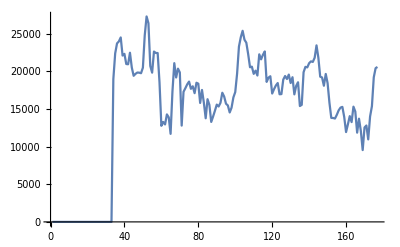

```mathematica
ListPlot[BC600["ci"],PlotRange->Full,Joined->True]
```

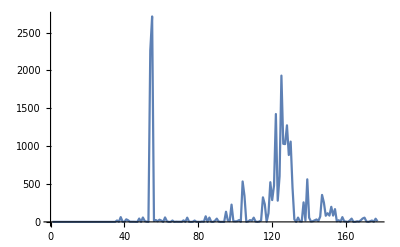

```mathematica
ListPlot[BC600["cs"],PlotRange->Full,Joined->True]
```

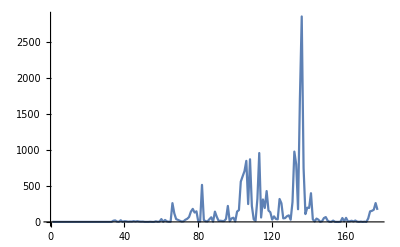

```mathematica
ListPlot[BC600["la"],PlotRange->Full,Joined->True]
```

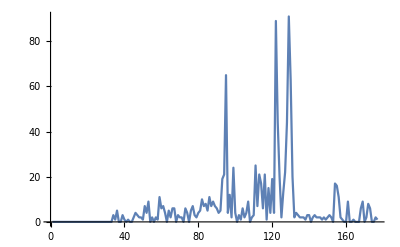

```mathematica
ListPlot[BC600["wk"],PlotRange->Full,Joined->True]
```

### Analysis 4 CKAN impact

ckanCRIDを含むグラフを抽出する。

すでに構成したハッシュとグラフのプロパティを当てる関数。ひとつでもあたればTrueを返す。
 ハッシュはログ中の位置を記述しており、リクエストパス・リファラーを分けたもの、Unionしたもの。

滞留時間をグラフから得る関数：

```mathematica
stayTime[g_Graph]:=Module[{elist,tlist},
elist=EdgeList[g];
tlist=Map[#[[3,1]]&,elist];
Max[tlist]-Min[tlist]
]
```

ckanCRIDを含むログの行とグラフのエッジにあるログの行を当てる関数 （T/F）:

```mathematica
logGraphQ[gr_Graph,asc_Association]:=Module[{elist,logposlist,res},
elist=EdgeList[gr];
logposlist=Map[#[[3,2]]&,elist];
res=Map[asc[#]&,logposlist];
Position[res,_Integer,{1}]/.{{}->False,{__}->True}
]
```

ckanCRIDをリクエストに含むノードをハイライトする関数：

```mathematica
toCRID[s_String/;StringMatchQ[s,RegularExpression["https://cir.nii.ac.jp/crid/.*"]]]:=StringTake[StringSplit[s,"/"][[5]],19]
```

```mathematica
ckanVertexHighlihgt[g_Graph,asc_Association]:=Module[{vlist,pos,targetv,op},
vlist=VertexList[g];
pos=Flatten[Position[Map[ckanCridPRACQ[toCRID[#]]&,VertexList[g]],True]];
targetv=vlist[[pos]];
op=VertexStyle->Map[#->Red&,targetv];
Graph[g,op]
]
```

CKAN - CRIDを含むグラフの抽出

```mathematica
(ckanGrP[4]=Map[If[logGraphQ[#[[3]],ckanCridPLogPosAC[4]],#,Null]&,storyGrIdxFlDs3[4]])//Dimensions
```

{158476}

```mathematica
(ckanGrR[4]=Map[If[logGraphQ[#[[3]],ckanCridRLogPosAC[4]],#,Null]&,storyGrIdxFlDs3[4]])//Dimensions
```

{158476}

```mathematica
(ckanGrPR[4]=Map[If[logGraphQ[#[[3]],ckanCridPRLogPosAC[4]],#,Null]&,storyGrIdxFlDs3[4]])//Dimensions
```

{158476}

```mathematica
(ckanGrPsel[4]=Cases[ckanGrP[4],{__},{1}])//Dimensions
```

{76,3}

```mathematica
ckanGrPselVL[4]=Map[VertexList[#[[3]]]&,ckanGrPsel[4]];
```

```mathematica
ckanGrPselEL[4]=Map[EdgeList[#[[3]]]&,ckanGrPsel[4]];
```

```mathematica
(ckanGrRsel[4]=Cases[ckanGrR[4],{__},{1}])//Dimensions
```

{6,3}

```mathematica
ckanGrRselVL[4]=Map[VertexList[#[[3]]]&,ckanGrRsel[4]];
```

```mathematica
ckanGrRselEL[4]=Map[EdgeList[#[[3]]]&,ckanGrRsel[4]];
```

```mathematica
(ckanGrPRsel[4]=Cases[ckanGrPR[4],{__},{1}])//Dimensions
```

{77,3}

```mathematica
ckanGrPRselVL[4]=Map[VertexList[#[[3]]]&,ckanGrPRsel[4]];
```

```mathematica
ckanGrPRselEL[4]=Map[EdgeList[#[[3]]]&,ckanGrPRsel[4]];
```

```mathematica
(ckanGrPRselHL[4]=Map[{#[[1]],#[[2]],ckanVertexHighlihgt[#[[3]],ckanCridPRACQ]}&,ckanGrPRsel[4]])//Dimensions
```

{77,3}

```mathematica
ckanGrPRVcount[4]=Map[VertexCount[#[[3]]]&,ckanGrPRselHL[4]]
```

{6,17,14,18,21,29,11,2,54,53,28,20,8,12,64,2,11,7,9,10,2,20,45,277,226,332,23,9,14,29,41,35,52,50,51,2,14,15,8,7,14,16,11,77,76,77,77,210,211,210,82,57,58,6,8,36,26,2,82,22,24,24,11,16,17,68,57,22,22,2,4,4,3,32,32,32,32}

```mathematica
accTimeList[g_Graph]:=Module[{elist,tlist},
elist=EdgeList[g];
tlist=Sort[Map[#[[3,1]]&,elist],#1>#2&]
]
```

```mathematica
timeSpan[tlist_]:=Map[(#[[1]]-#[[2]])&,Partition[tlist,2,1]]
```

```mathematica
ckanGrPRstayTime[4]=Map[stayTime[#[[3]]]&,ckanGrPRselHL[4]]
```

{35763.,413.,2255.,451.,749.,21460.,414.,0.,2420.,2141.,4910.,7132.,184.,481.,3505.,0.,67.,254.,318.,161.,0.,1532.,11779.,1272.,1238.,1182.,1104.,2557.,1541.,6977.,25019.,25019.,40621.,37531.,37531.,0.,1731.,1752.,6999.,3265.,3727.,375.,185.,25862.,25832.,25832.,25832.,26855.,26842.,26842.,3934.,7947.,18844.,68.,97.,10174.,1985.,0.,2132.,900.,7392.,7418.,255.,1364.,15218.,5384.,4099.,1390.,1352.,14.,136.,7.,13.,13877.,13807.,13807.,3345.}

### Analysis 5 CKAN graph reform

program :

可能な全Vertexにアクセス時間リストを付与：

```mathematica
gatherDistributeUniq[l_]:=Module[{first,target},
first=l[[1,1]];
target=Map[#[[2]]&,l];
{first,target}
]
```

```mathematica
gatherDistributeUniqRl[l_]:=Module[{first,target},
first=l[[1,1]];
target=Map[#[[2]]&,l];
first->{first,target}
]
```

```mathematica
addVertexAccTime[g_]:=Module[{gatherTimeV,gatherTimeVRl},
gatherTimeV=Gather[Map[{#[[2]],#[[3,1]]}&,EdgeList[g]],#1[[1]]==#2[[1]]&];
gatherTimeVRl=Map[gatherDistributeUniqRl,gatherTimeV];
VertexReplace[g,gatherTimeVRl]
]
```

```mathematica
guessVertexCoorGr[g_,timeshift_]:=Module[{allAccTime,baseTime,repPos,target,repRl},
allAccTime=Cases[Flatten[Map[#[[2]]&,g//VertexList]],_Real];
baseTime=Min[allAccTime]+timeshift;
repPos=Flatten[Position[Map[Head,VertexList[g]],String]];
target=Map[VertexList[g][[#]]&,repPos];
repRl=Map[#->{#,{baseTime}}&,target];
VertexReplace[g,repRl]
]
```

```mathematica
accTimeMinGr[g_]:=Min[Cases[Flatten[Map[#[[2]]&,g//VertexList]],_Real]]
```

```mathematica
reformCoorGr[g_,baseTime_,f_]:=f[Map[{Max[#[[2]]],Min[#[[2]]]}&,VertexList[g]]-baseTime]
```

```mathematica
timeLineGr[g_,timeshift_,f_]:=Module[{gnew,btime,coornew},
gnew=guessVertexCoorGr[g,timeshift];
btime=accTimeMinGr[gnew];
coornew=reformCoorGr[gnew,btime,Sqrt];
Graph[gnew,VertexSize->Automatic,VertexCoordinates->coornew]
]
```

```mathematica
(ckanGrPRselHLAT[4]=Map[{#[[1]],#[[2]],addVertexAccTime[#[[3]]]}&,ckanGrPRselHL[4]])//Dimensions
```

{77,3}

ロググループ：

```mathematica
loggroupCKAN=Map[#[[2]]&,ckanGrPRselHLAT[4]]
```

{{100,1},{385,1},{1044,1},{2732,1},{3868,1},{9427,1},{15977,1},{19788,1},{19797,1},{19797,1},{20912,1},{21418,1},{24567,1},{31557,1},{32248,1},{32445,1},{34747,1},{39730,1},{40025,1},{41198,1},{41206,1},{43772,1},{44109,1},{46287,1},{46287,1},{46288,1},{47020,1},{51848,1},{51848,1},{51902,1},{52293,1},{52293,1},{54345,1},{54345,1},{54345,1},{55056,1},{55392,1},{55392,1},{55506,1},{58965,1},{60413,1},{62867,1},{64071,1},{64769,1},{64769,1},{64769,1},{64769,1},{71034,1},{71034,1},{71034,1},{74412,1},{76087,1},{76087,1},{76331,1},{83394,1},{94470,1},{94476,1},{97575,1},{101697,1},{101698,1},{102006,1},{102006,1},{105014,1},{128240,1},{132304,1},{135351,1},{135351,1},{136023,1},{136023,1},{136353,1},{139415,1},{139421,1},{140452,1},{143059,1},{143059,1},{143059,1},{143162,1}}

ノードの数え上げ：

```mathematica
vcCKAN=Map[VertexCount[#[[3]]]&,ckanGrPRselHLAT[4]]
```

{6,17,14,18,21,29,11,2,54,53,28,20,8,12,64,2,11,7,9,10,2,20,45,277,226,332,23,9,14,29,41,35,52,50,51,2,14,15,8,7,14,16,11,77,76,77,77,210,211,210,82,57,58,6,8,36,26,2,82,22,24,24,11,16,17,68,57,22,22,2,4,4,3,32,32,32,32}

エッジの数え上げ：

```mathematica
ecCKAN=Map[EdgeCount[#[[3]]]&,ckanGrPRselHLAT[4]]
```

{5,22,19,29,36,38,15,1,133,111,44,25,9,20,78,1,17,10,10,23,1,27,55,453,367,546,39,15,22,39,51,48,71,63,64,1,30,32,11,7,24,22,10,136,135,136,136,368,337,339,106,118,118,6,9,78,84,1,129,47,45,44,10,32,21,171,147,44,43,2,7,3,2,39,38,40,69}

アクセス時刻：

```mathematica
(accCKAN=Map[Map[#[[3,1]]&,EdgeList[#[[3]]]]&,ckanGrPRselHLAT[4]])//Dimensions
```

{77}

最大滞在時間：

```mathematica
maxTimeSpan[l_]:=Max[Map[#[[1]]-#[[2]]&,Partition[Sort[l,#1>#2&],2,1]]]
```

```mathematica
(maxtimespanCKAN=Map[maxTimeSpan,accCKAN]/.{-Infinity->0})/60
```

{343.367,1.53333,24.6667,1.78333,2.03333,91.5667,1.76667,0,5.53333,6.01667,17.2333,115.,0.883333,2.63333,12.2333,0,0.25,2.05,3.95,0.666667,0,6.51667,71.5,0.45,0.45,2.65,5.48333,39.3,12.4333,106.15,207.,206.967,566.15,566.15,566.15,0,20.9,20.9,110.367,30.6,41.6333,1.36667,1.15,291.183,291.183,291.183,291.183,360.1,361.15,361.15,4.96667,23.3833,158.567,0.416667,0.333333,100.1,13.5667,0,8.41667,3.88333,69.9667,69.9667,1.15,15.05,179.567,10.2,10.2,11.0833,11.0833,0.233333,1.78333,0.0666667,0.216667,146.917,146.733,146.917,49.3333}

滞留時間：

```mathematica
staytimeCKAN=Map[Max[#]-Min[#]&,accCKAN]
```

{35763.,413.,2255.,451.,749.,21460.,414.,0.,2420.,2141.,4910.,7132.,184.,481.,3505.,0.,67.,254.,318.,161.,0.,1532.,11779.,1272.,1238.,1182.,1104.,2557.,1541.,6977.,25019.,25019.,40621.,37531.,37531.,0.,1731.,1752.,6999.,3265.,3727.,375.,185.,25862.,25832.,25832.,25832.,26855.,26842.,26842.,3934.,7947.,18844.,68.,97.,10174.,1985.,0.,2132.,900.,7392.,7418.,255.,1364.,15218.,5384.,4099.,1390.,1352.,14.,136.,7.,13.,13877.,13807.,13807.,3345.}

```mathematica
staytimeCKAN/60
```

{596.05,6.88333,37.5833,7.51667,12.4833,357.667,6.9,0.,40.3333,35.6833,81.8333,118.867,3.06667,8.01667,58.4167,0.,1.11667,4.23333,5.3,2.68333,0.,25.5333,196.317,21.2,20.6333,19.7,18.4,42.6167,25.6833,116.283,416.983,416.983,677.017,625.517,625.517,0.,28.85,29.2,116.65,54.4167,62.1167,6.25,3.08333,431.033,430.533,430.533,430.533,447.583,447.367,447.367,65.5667,132.45,314.067,1.13333,1.61667,169.567,33.0833,0.,35.5333,15.,123.2,123.633,4.25,22.7333,253.633,89.7333,68.3167,23.1667,22.5333,0.233333,2.26667,0.116667,0.216667,231.283,230.117,230.117,55.75}

```mathematica
f[x_]=Log[x+1]
```

Log[1+x]

```mathematica
(ckanGrPRselHLTL[4]=Map[timeLineGr[#[[3]],-60,f]&,ckanGrPRselHLAT[4]])//Dimensions
```

Part::partd: Part specification https://www.google.com/⟦2⟧ is longer than depth of object.

Part::partd: Part specification https://www.bing.com/⟦2⟧ is longer than depth of object.

Part::partd: Part specification https://cn.bing.com/⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{77}

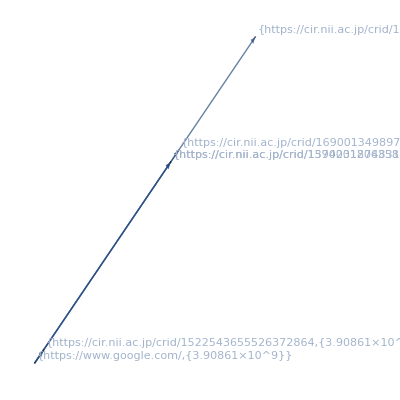

```mathematica
ckanGrPRselHLTL[4][[1]]
```

### Analysis 6 CKAN voc-graph

vocRlの読み込み：

```mathematica
vocRlFiles=FileNames[vocdir<>"/*.wl"]
```

{/Volumes/home/NII/togo-log/rcoslogs/voc/voc_path_action_ci_rl.wl,/Volumes/home/NII/togo-log/rcoslogs/voc/voc_path_action_cs_rl.wl,/Volumes/home/NII/togo-log/rcoslogs/voc/voc_path_action_la_rl.wl,/Volumes/home/NII/togo-log/rcoslogs/voc/voc_path_action_wk_rl.wl,/Volumes/home/NII/togo-log/rcoslogs/voc/voc_ref_action_ci_rl.wl,/Volumes/home/NII/togo-log/rcoslogs/voc/voc_ref_action_cs_rl.wl,/Volumes/home/NII/togo-log/rcoslogs/voc/voc_ref_action_la_rl.wl,/Volumes/home/NII/togo-log/rcoslogs/voc/voc_ref_action_wk_rl.wl}

```mathematica
vocRlList=Map[Get,vocRlFiles];
```

```mathematica
(vocRl["all:path"]=Apply[Join,vocRlList])//Dimensions
```

{113}

```mathematica
vocRl["all:path"][[1]]
```

x_/;StringMatchQ[x,RegularExpression[https://cir.nii.ac.jp/]]→voc[ci:top]

===== /プログラム検討 =====

====== /引数 ======

```mathematica
gr=ckanGrPRselHLTL[4][[1]]
```

-Graphics-

```mathematica
rl=vocRl["all:path"];
```

====== 引数/ ======

====== /内部変数 ======

```mathematica
vl=VertexList[gr]
```

{{https://cir.nii.ac.jp/crid/1574231874831099776?lang=en,{3.90862×10^9}},{https://cir.nii.ac.jp/crid/1390001206358757632,{3.90862×10^9}},{https://www.google.com/,{3.90861×10^9}},{https://cir.nii.ac.jp/crid/1522543655526372864,{3.90861×10^9}},{https://cir.nii.ac.jp/crid/1690013498979934208,{3.90862×10^9}},{https://cir.nii.ac.jp/crid/1582543029414514048,{3.90864×10^9}}}

```mathematica
vname=Map[#[[1]]&,vl]
```

{https://cir.nii.ac.jp/crid/1574231874831099776?lang=en,https://cir.nii.ac.jp/crid/1390001206358757632,https://www.google.com/,https://cir.nii.ac.jp/crid/1522543655526372864,https://cir.nii.ac.jp/crid/1690013498979934208,https://cir.nii.ac.jp/crid/1582543029414514048}

```mathematica
vrename=(vname/.rl)
```

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[List,RegularExpression[https://cir.nii.ac.jp/]].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[List,RegularExpression[https://cir.nii.ac.jp/ja]].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[List,RegularExpression[https://cir.nii.ac.jp/\?.*]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

{voc[ci:detail],voc[ci:detail],https://www.google.com/,voc[ci:detail],voc[ci:detail],voc[ci:detail]}

```mathematica
vrenameRl=Map[Apply[Rule,#]&,Transpose[{vl,vrename}]]
```

{{https://cir.nii.ac.jp/crid/1574231874831099776?lang=en,{3.90862×10^9}}→voc[ci:detail],{https://cir.nii.ac.jp/crid/1390001206358757632,{3.90862×10^9}}→voc[ci:detail],{https://www.google.com/,{3.90861×10^9}}→https://www.google.com/,{https://cir.nii.ac.jp/crid/1522543655526372864,{3.90861×10^9}}→voc[ci:detail],{https://cir.nii.ac.jp/crid/1690013498979934208,{3.90862×10^9}}→voc[ci:detail],{https://cir.nii.ac.jp/crid/1582543029414514048,{3.90864×10^9}}→voc[ci:detail]}

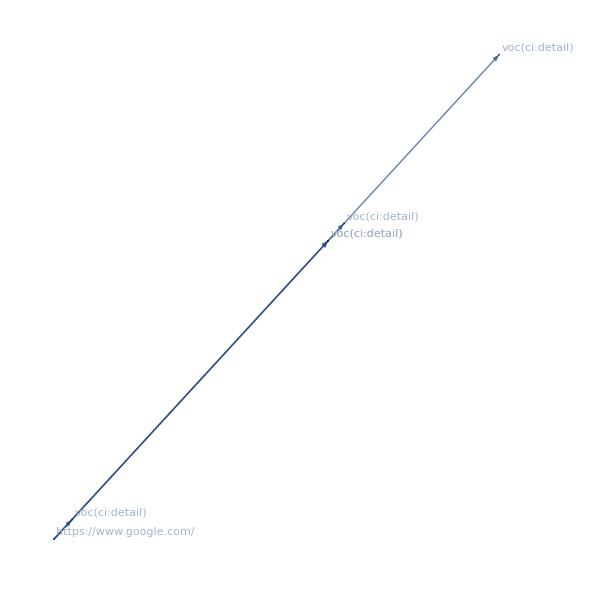

```mathematica
Graph[gr,VertexLabels->vrenameRl]
```

====== 内部変数/ ======

===== プログラム検討/ =====

```mathematica
toVocGraph[gr_,rl_]:=Module[{vl,vname,vrename,vrenameRl},
Print["it may cause StringMatchQ warn."];
vl=VertexList[gr];
vname=Map[#[[1]]&,vl];
vrename=(vname/.rl);
vrenameRl=Map[Apply[Rule,#]&,Transpose[{vl,vrename}]];
Graph[gr,VertexLabels->vrenameRl]
]
```

it may cause StringMatchQ warn.

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[List,RegularExpression[https://cir.nii.ac.jp/]].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[List,RegularExpression[https://cir.nii.ac.jp/ja]].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[List,RegularExpression[https://cir.nii.ac.jp/\?.*]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

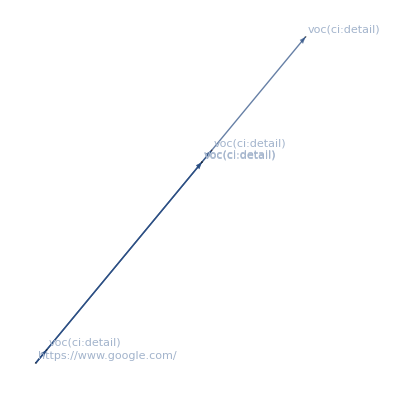

```mathematica
toVocGraph[ckanGrPRselHLTL[4][[1]],vocRl["all:path"]]
```

it may cause StringMatchQ warn.

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[List,RegularExpression[https://cir.nii.ac.jp/]].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[List,RegularExpression[https://cir.nii.ac.jp/ja]].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[List,RegularExpression[https://cir.nii.ac.jp/\?.*]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

it may cause StringMatchQ warn.

it may cause StringMatchQ warn.

it may cause StringMatchQ warn.

«73 more identical outputs»

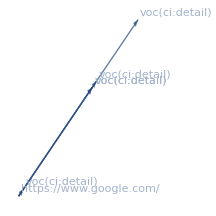
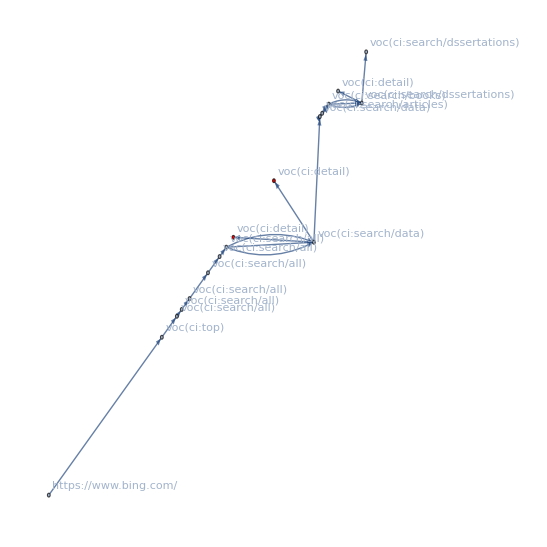
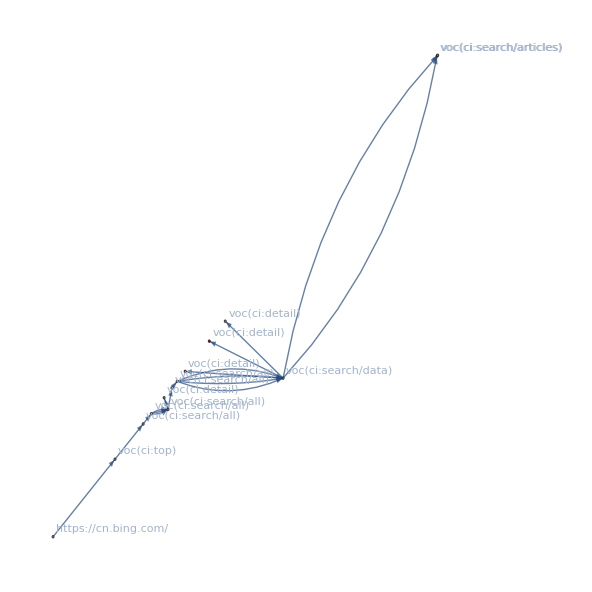
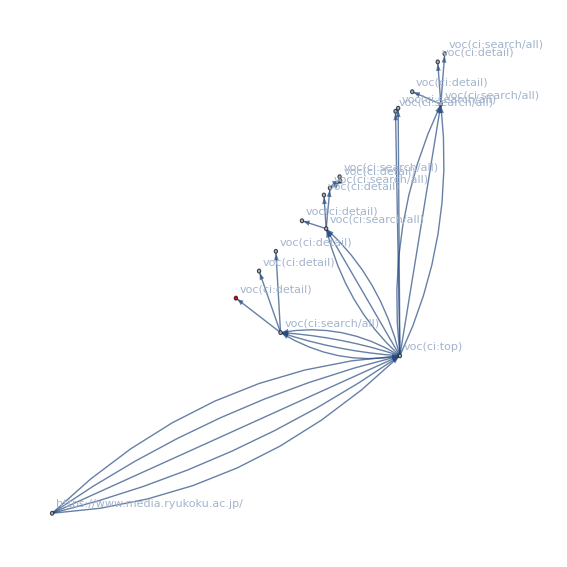
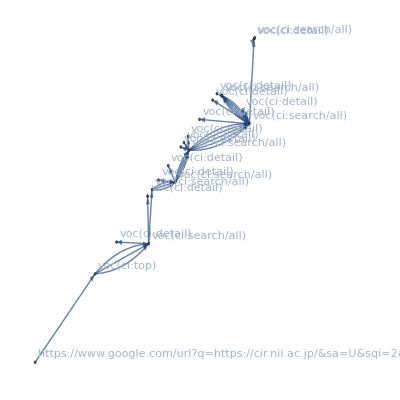
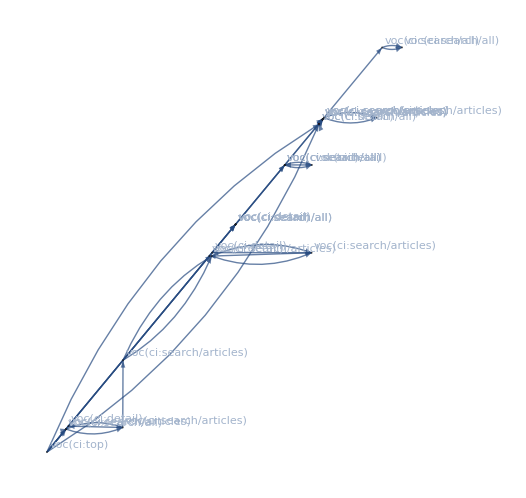
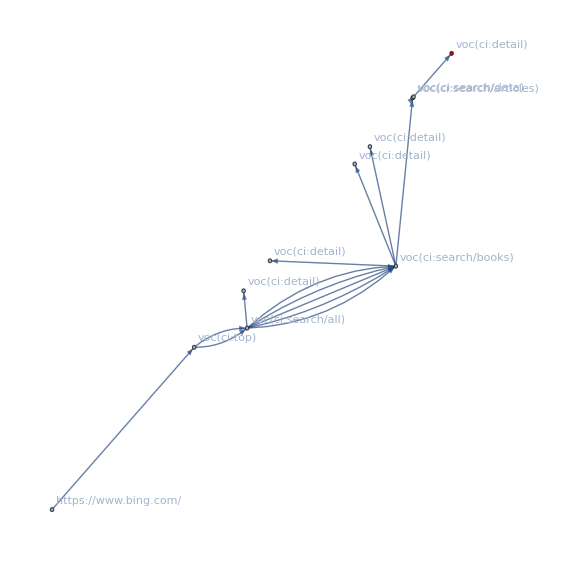
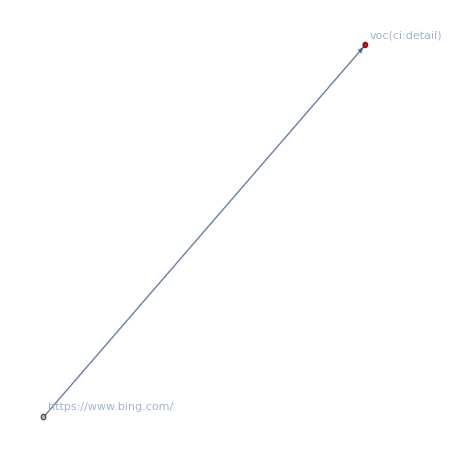
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

```mathematica
Map[toVocGraph[#,vocRl["all:path"]]&,ckanGrPRselHLTL[4]]//TableForm
```

### Report:CKAN impact

```mathematica
logtbl={{"- ログ件数 -","述べログ件数"},{{"全件数","ユーザーアクセス件数"},{ToExpression[StringSplit[logwc][[1]]],idxLogLen[4]}}}//TableForm
```

- ログ件数 - | 述べログ件数
全件数
ユーザーアクセス件数 | 20753167
2660456

```mathematica
ckanlogtbl={{"- CKAN-cridを含むログ件数 -","述べログ件数","cridのユニーク件数"},{{"リクエストにCKAN-crid含む","リファラーにCKAN-crid含む","いずれか含む"},{ckanCridPLogPos[4]//Length,ckanCridRLogPos[4]//Length,ckanCridPRLogPos[4]//Length},{Union[ckanCridPlist]//Length,Union[ckanCridRlist]//Length,ckanCridPRU//Length}}}//TableForm
```

- CKAN-cridを含むログ件数 - | 述べログ件数 | cridのユニーク件数
リクエストにCKAN-crid含む
リファラーにCKAN-crid含む
いずれか含む | 228
7
235 | 185
6
185

```mathematica
ckanchaintbl={{"- アクション連鎖数 -","件数"},{{"全件数","ノードにCKAN-crid含む"},{storyGrIdxFlDs3[4]//Length,ckanGrPRselHL[4]//Length}}}//TableForm
```

- アクション連鎖数 - | 件数
全件数
ノードにCKAN-crid含む | 158476
77

```mathematica
ckangrsummarytbl={{"アクセスグラフ通し番号","ロググループ","ノード数","エッジ数","最大滞在時間(分)","滞留時間(分)"},{Table[i,{i,Length[loggroupCKAN]}],loggroupCKAN,vcCKAN,ecCKAN,maxtimespanCKAN/60,staytimeCKAN/60}}//TableForm
```

アクセスグラフ通し番号 | ロググループ | ノード数 | エッジ数 | 最大滞在時間(分) | 滞留時間(分)
1
2
3
4
5
6
7
8
9
10
11
12
13
14
15
16
17
18
19
20
21
22
23
24
25
26
27
28
29
30
31
32
33
34
35
36
37
38
39
40
41
42
43
44
45
46
47
48
49
50
51
52
53
54
55
56
57
58
59
60
61
62
63
64
65
66
67
68
69
70
71
72
73
74
75
76
77 | 100 | 1
385 | 1
1044 | 1
2732 | 1
3868 | 1
9427 | 1
15977 | 1
19788 | 1
19797 | 1
19797 | 1
20912 | 1
21418 | 1
24567 | 1
31557 | 1
32248 | 1
32445 | 1
34747 | 1
39730 | 1
40025 | 1
41198 | 1
41206 | 1
43772 | 1
44109 | 1
46287 | 1
46287 | 1
46288 | 1
47020 | 1
51848 | 1
51848 | 1
51902 | 1
52293 | 1
52293 | 1
54345 | 1
54345 | 1
54345 | 1
55056 | 1
55392 | 1
55392 | 1
55506 | 1
58965 | 1
60413 | 1
62867 | 1
64071 | 1
64769 | 1
64769 | 1
64769 | 1
64769 | 1
71034 | 1
71034 | 1
71034 | 1
74412 | 1
76087 | 1
76087 | 1
76331 | 1
83394 | 1
94470 | 1
94476 | 1
97575 | 1
101697 | 1
101698 | 1
102006 | 1
102006 | 1
105014 | 1
128240 | 1
132304 | 1
135351 | 1
135351 | 1
136023 | 1
136023 | 1
136353 | 1
139415 | 1
139421 | 1
140452 | 1
143059 | 1
143059 | 1
143059 | 1
143162 | 1 | 6
17
14
18
21
29
11
2
54
53
28
20
8
12
64
2
11
7
9
10
2
20
45
277
226
332
23
9
14
29
41
35
52
50
51
2
14
15
8
7
14
16
11
77
76
77
77
210
211
210
82
57
58
6
8
36
26
2
82
22
24
24
11
16
17
68
57
22
22
2
4
4
3
32
32
32
32 | 5
22
19
29
36
38
15
1
133
111
44
25
9
20
78
1
17
10
10
23
1
27
55
453
367
546
39
15
22
39
51
48
71
63
64
1
30
32
11
7
24
22
10
136
135
136
136
368
337
339
106
118
118
6
9
78
84
1
129
47
45
44
10
32
21
171
147
44
43
2
7
3
2
39
38
40
69 | 343.367
1.53333
24.6667
1.78333
2.03333
91.5667
1.76667
0
5.53333
6.01667
17.2333
115.
0.883333
2.63333
12.2333
0
0.25
2.05
3.95
0.666667
0
6.51667
71.5
0.45
0.45
2.65
5.48333
39.3
12.4333
106.15
207.
206.967
566.15
566.15
566.15
0
20.9
20.9
110.367
30.6
41.6333
1.36667
1.15
291.183
291.183
291.183
291.183
360.1
361.15
361.15
4.96667
23.3833
158.567
0.416667
0.333333
100.1
13.5667
0
8.41667
3.88333
69.9667
69.9667
1.15
15.05
179.567
10.2
10.2
11.0833
11.0833
0.233333
1.78333
0.0666667
0.216667
146.917
146.733
146.917
49.3333 | 596.05
6.88333
37.5833
7.51667
12.4833
357.667
6.9
0.
40.3333
35.6833
81.8333
118.867
3.06667
8.01667
58.4167
0.
1.11667
4.23333
5.3
2.68333
0.
25.5333
196.317
21.2
20.6333
19.7
18.4
42.6167
25.6833
116.283
416.983
416.983
677.017
625.517
625.517
0.
28.85
29.2
116.65
54.4167
62.1167
6.25
3.08333
431.033
430.533
430.533
430.533
447.583
447.367
447.367
65.5667
132.45
314.067
1.13333
1.61667
169.567
33.0833
0.
35.5333
15.
123.2
123.633
4.25
22.7333
253.633
89.7333
68.3167
23.1667
22.5333
0.233333
2.26667
0.116667
0.216667
231.283
230.117
230.117
55.75

### Export:CKAN impact

```mathematica
(ckanEL=Map[MapApply[List,EdgeList[#]]&,ckanGrPRselHLTL[4]])//Dimensions
```

{77}

```mathematica
ckanELexp=Map[{#[[1,1]],#[[2,1]]}&,ckanEL,{2}];
```

```mathematica
expdir=mountdir<>"log/D="<>date<>"/T=4/_story"
```

/Volumes/home/NII/togo-log/rcoslogs/log/D=20231110/T=4/_story

```mathematica
SetDirectory[expdir]
```

/Volumes/home/NII/togo-log/rcoslogs/log/D=20231110/T=4/_story

```mathematica
Export["ckanedgelist.json",ckanELexp]
```

ckanedgelist.json

## 終端処理

```mathematica
end=AbsoluteTime[Date[]]
```

3.910108895129774×10^9

```mathematica
end-start
```

79.748462